Using the usual formulation to propagate Twiss isn’t working, presumably because of the energy change. Let’s take a dumber approach

```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.csv"];
raw=raw[[2;;]];

ListPointPlot3D[{
raw[[All,{1,2,3}]],
raw[[All,{1,2,4}]]
}
]
```

-Graphics3D-

```mathematica
interpBeta = Interpolation[raw[[All,{1,2,3}]],InterpolationOrder->2]
interpAlpha = Interpolation[raw[[All,{1,2,4}]],InterpolationOrder->2]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000408571,-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.,2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

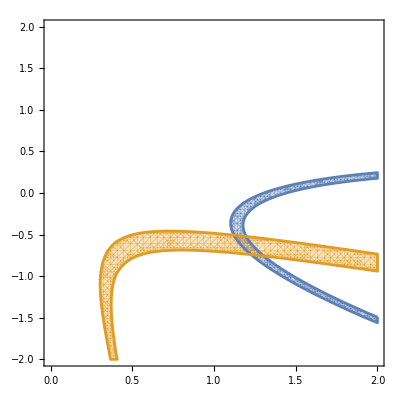

```mathematica
targetBeta = 3.0;
targetAlpha = 0.1;
tolerance = 0.1;
RegionPlot[{
Abs[interpBeta[beta,alpha]-targetBeta]<tolerance,
Abs[interpAlpha[beta,alpha]-targetAlpha]<tolerance
},
{beta,0,2},
{alpha,-2,2},
PlotPoints->50
]
```

```mathematica
deg = 3;
expr = Sum[Subscript[a, i,j] x^i y^j,{i,0,deg},{j,0,deg}]
coeffs = Flatten[Table[ Subscript[a, i,j],{i,0,deg},{j,0,deg}]]

nlm = NonlinearModelFit[
raw[[All,{1,2,3}]],
expr,
coeffs,
{x,y}
]
nlm["RSquared"]
```

a_(0,0)+y a_(0,1)+y^2 a_(0,2)+y^3 a_(0,3)+x a_(1,0)+x y a_(1,1)+x y^2 a_(1,2)+x y^3 a_(1,3)+x^2 a_(2,0)+x^2 y a_(2,1)+x^2 y^2 a_(2,2)+x^2 y^3 a_(2,3)+x^3 a_(3,0)+x^3 y a_(3,1)+x^3 y^2 a_(3,2)+x^3 y^3 a_(3,3)

{a_(0,0),a_(0,1),a_(0,2),a_(0,3),a_(1,0),a_(1,1),a_(1,2),a_(1,3),a_(2,0),a_(2,1),a_(2,2),a_(2,3),a_(3,0),a_(3,1),a_(3,2),a_(3,3)}

FittedModel[…]

0.947206